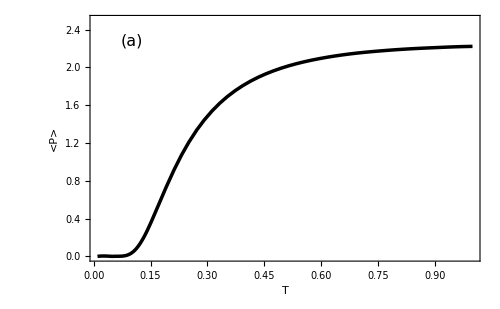

```mathematica
t1=Plot[Interpolation[{{0.01,1.53897*10^-25},{0.05,0.0000213761},{0.08,0.00525274},{0.09,0.0155061},{0.095,0.0243419},{0.1,0.0363221},{0.108,0.062942},{0.115,0.0942893},{0.125,0.151961},{0.15,0.3485},{0.175,0.58125},{0.2,0.811626},{0.225,1.02023},{0.235,1.09598},{0.25,1.20093},{0.275,1.35444},{0.3,1.48314},{0.325,1.5913},{0.35,1.68193},{0.375,1.75834},{0.38,1.77209},{0.4,1.82282},{0.425,1.87765},{0.5,1.99873},{0.55,2.05416},{0.6,2.09612},{0.65,2.12875},{0.7,2.15372},{0.75,2.17245},{0.8,2.18794},{0.85,2.19992},{0.9,2.20914},{0.95,2.21745},{1,2.22257}}][x],{x,0.01,1},Frame->True,FrameStyle->Directive[Black,Thin,FontFamily->"Times New Roman"],PlotStyle->{{Black,Thickness[0.005]}},BaseStyle->{Black,FontSize->17},PlotRange->{{0.01,1},{0,2.5}},FrameLabel->{Style["T",15,Black,Italic],Style["<P>",15,Black,Italic]},Epilog->{Text[Style["(a)",FontSize->16,FontFamily->"Times New Roman"],{0.1,2.2},{Center,Bottom}]},ImageSize->{500,300}]
```

```mathematica
data={{0.01,1.53897*10^-25},{0.05,0.0000213761},{0.08,0.00525274},{0.09,0.0155061},{0.095,0.0243419},{0.1,0.0363221},{0.108,0.062942},{0.115,0.0942893},{0.125,0.151961},{0.15,0.3485},{0.175,0.58125},{0.2,0.811626},{0.225,1.02023},{0.235,1.09598},{0.25,1.20093},{0.275,1.35444},{0.3,1.48314},{0.325,1.5913},{0.35,1.68193},{0.375,1.75834},{0.38,1.77209},{0.4,1.82282},{0.425,1.87765},{0.5,1.99873},{0.55,2.05416},{0.6,2.09612},{0.65,2.12875},{0.7,2.15372},{0.75,2.17245},{0.8,2.18794},{0.85,2.19992},{0.9,2.20914},{0.95,2.21745},{1,2.22257}};

(*定义插值函数*)
interpFunc=Interpolation[data];

(*计算导数*)
slopeFunc=D[interpFunc[x],x];

(*在从最小到最大值每间隔 0.01 计算斜率*)
xValues=Range[0.01,1,0.01];
slopes=Table[slopeFunc/. x->xVal,{xVal,xValues}];

(*找到最大斜率及其对应的 T 值*)
maxSlope=Max[slopes];
maxIndex=FirstPosition[slopes,maxSlope];
maxT=xValues[[maxIndex]];

(*输出所有的斜率值*)
TableForm[Transpose[{xValues,slopes}],TableHeadings->{None,{"T","Slope"}}]

(*输出最大斜率值及其对应的 T 值*)
Print["最大斜率值: ",maxSlope]
Print["对应的 T 值: ",maxT]
```

T | Slope
0.01 | 0.55886
0.02 | 0.162257
0.03 | -0.0934178
0.04 | -0.208164
0.05 | -0.181983
0.06 | 0.0242639
0.07 | 0.13662
0.08 | 0.624723
0.09 | 1.4863
0.1 | 2.73482
0.11 | 4.24947
0.12 | 5.76806
0.13 | 7.08764
0.14 | 8.17027
0.15 | 8.84301
0.16 | 9.29892
0.17 | 9.50788
0.18 | 9.35733
0.19 | 9.1952
0.2 | 8.90892
0.21 | 8.45594
0.22 | 8.03921
0.23 | 7.57558
0.24 | 7.10802
0.25 | 6.66262
0.26 | 6.24084
0.27 | 5.82949
0.28 | 5.42067
0.29 | 5.05104
0.3 | 4.70873
0.31 | 4.39813
0.32 | 4.09838
0.33 | 3.81614
0.34 | 3.55685
0.35 | 3.32759
0.36 | 3.10641
0.37 | 2.89792
0.38 | 2.70395
0.39 | 2.53468
0.4 | 2.37481
0.41 | 2.22588
0.42 | 2.08788
0.43 | 1.95534
0.44 | 1.83344
0.45 | 1.72075
0.46 | 1.61726
0.47 | 1.52298
0.48 | 1.4379
0.49 | 1.36203
0.5 | 1.29536
0.51 | 1.20719
0.52 | 1.13709
0.53 | 1.07161
0.54 | 1.01078
0.55 | 0.95458
0.56 | 0.907876
0.57 | 0.858964
0.58 | 0.813364
0.59 | 0.771076
0.6 | 0.7321
0.61 | 0.703681
0.62 | 0.668365
0.63 | 0.634385
0.64 | 0.601741
0.65 | 0.570433
0.66 | 0.541195
0.67 | 0.512259
0.68 | 0.484459
0.69 | 0.457795
0.7 | 0.427
0.71 | 0.40324
0.72 | 0.38188
0.73 | 0.36292
0.74 | 0.34636
0.75 | 0.3322
0.76 | 0.330032
0.77 | 0.316748
0.78 | 0.303248
0.79 | 0.289532
0.8 | 0.2756
0.81 | 0.25846
0.82 | 0.24532
0.83 | 0.23278
0.84 | 0.22084
0.85 | 0.2095
0.86 | 0.195533
0.87 | 0.186713
0.88 | 0.179373
0.89 | 0.173513
0.9 | 0.169133
0.91 | 0.178348
0.92 | 0.171972
0.93 | 0.163772
0.94 | 0.153748
0.95 | 0.1419
0.96 | 0.128228
0.97 | 0.112732
0.98 | 0.095412
0.99 | 0.076268
1. | 0.0553

最大斜率值: 9.50788

对应的 T 值: {0.17}

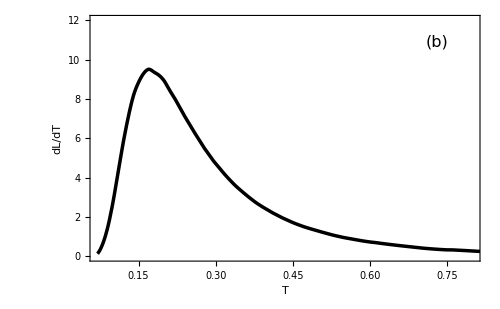

$UserDocumentsDirectory\slope.csv

```mathematica
t2=Plot[Interpolation[{{0.01,0.55886},{0.02,0.162257},{0.03,-0.0934178},{0.04,-0.208164},{0.05,-0.181983},{0.06,0.0242639},{0.07,0.13662},{0.08,0.624723},{0.09,1.4863},{0.1,2.73482},{0.11,4.24947},{0.12,5.76806},{0.13,7.08764},{0.14,8.17027},{0.15,8.84301},{0.16,9.29892},{0.17,9.50788},{0.18,9.35733},{0.19,9.1952},{0.2,8.90892},{0.21,8.45594},{0.22,8.03921},{0.23,7.57558},{0.24,7.10802},{0.25,6.66262},{0.26,6.24084},{0.27,5.82949},{0.28,5.42067},{0.29,5.05104},{0.3,4.70873},{0.31,4.39813},{0.32,4.09838},{0.33,3.81614},{0.34,3.55685},{0.35,3.32759},{0.36,3.10641},{0.37,2.89792},{0.38,2.70395},{0.39,2.53468},{0.4,2.37481},{0.41,2.22588},{0.42,2.08788},{0.43,1.95534},{0.44,1.83344},{0.45,1.72075},{0.46,1.61726},{0.47,1.52298},{0.48,1.4379},{0.49,1.36203},{0.5,1.29536},{0.51,1.20719},{0.52,1.13709},{0.53,1.07161},{0.54,1.01078},{0.55,0.95458},{0.56,0.907876},{0.57,0.858964},{0.58,0.813364},{0.59,0.771076},{0.6,0.7321},{0.61,0.703681},{0.62,0.668365},{0.63,0.634385},{0.64,0.601741},{0.65,0.570433},{0.66,0.541195},{0.67,0.512259},{0.68,0.484459},{0.69,0.457795},{0.7,0.427},{0.71,0.40324},{0.72,0.38188},{0.73,0.36292},{0.74,0.34636},{0.75,0.3322},{0.76,0.330032},{0.77,0.316748},{0.78,0.303248},{0.79,0.289532},{0.8,0.2756},{0.81,0.25846},{0.82,0.24532},{0.83,0.23278},{0.84,0.22084},{0.85,0.2095},{0.86,0.195533},{0.87,0.186713},{0.88,0.179373},{0.89,0.173513},{0.9,0.169133},{0.91,0.178348},{0.92,0.171972},{0.93,0.163772},{0.94,0.153748},{0.95,0.1419},{0.96,0.128228},{0.97,0.112732},{0.98,0.095412},{0.99,0.076268},{1.,0.0553}}][x],{x,0.07,1},Frame->True,FrameStyle->Directive[Black,Thin,FontFamily->"Times New Roman"],PlotStyle->{{Black,Thickness[0.005]}},BaseStyle->{Black,FontSize->17},PlotRange->{{0.07,0.8},{0,12}},FrameLabel->{Style["T",15,Black,Italic],Style["dL/dT",15,Black,Italic]},Epilog->{Text[Style["(b)",FontSize->16,FontFamily->"Times New Roman"],{0.73,10.5},{Center,Bottom}]},ImageSize->{500,300}]
```

```mathematica
"
```

Export::filex: 文件 "C:\Users\dwc\Documents\slope_data.csv" 已经存在.

$Failed

Export::filex: 文件 "C:\Users\dwc\Documents\slope_data_with_header.csv" 已经存在.

$Failed

General::prng: 选项值 PlotRange -> {{0.07,0.8},{0,12},PlotLegends→Placed[LineLegend[{Our paper}],{0.8,0.9}],FrameLabel→{T,L}} 不是 All、Full、Automatic、一个机器精度正数，或者由范围指定组成的恰当列表.

ListLinePlot::nonopt: ListLinePlot[{0.01,7.91348×10^-27},{0.03,7.91348×10^-10},{0.04,1.11027×10^-8},{0.05,0.0000111027},«4»,{0.1,0.0275874},{0.108,0.0447274},«27»] 中位置 1 外应该是选项（而不是 {0.7,0.169082}）. 选项必须是一个规则或者规则列表.